Problem I : introduction of a new product

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; 
h[x_,r_,μ_,σ_,θ_,α_,δ_,k_]:=(θ- α k) k *x/(r-μ)-δ k;
Kopt=(θ x-δ(r-μ))/(2 α x);
hC[x_,r_,μ_,σ_,θ_,α_,δ_]:=(x θ-δ (r-μ))^2/(4 α (r-μ)x);
```

## Benchmark Model

S/ capacidade optimizada :

```mathematica
xB[μ_,σ_,r_,θ_,k_,α_,δ_]:=(d1[μ,σ,r])/(d1[μ,σ,r]-1) δ (r-μ)/(θ- α k);
xB2[μ_,σ_,r_,θ_,k_,α_,δ_]:=(d1[μ,σ,r]+1)/(d1[μ,σ,r]-1) δ (r-μ)/(θ- α k); (* raiz inválida -> para x \in C, h(x)>F(x) ; não dedutível analiticamente *)
aB[x_,μ_,σ_,r_,θ_,k_,α_,δ_]:=((θ- α k) k *x/(r-μ)-δ k)*x^(-d1[μ,σ,r]);
FxB[x_,r_,μ_,σ_,θ_,α_,δ_,k_]:=If[x<xB[μ,σ,r,θ,k,α,δ],
aB[xB[μ,σ,r,θ,k,α,δ],μ,σ,r,θ,k,α,δ]*x^(d1[μ,σ,r]),
h[x,r,μ,σ,θ,α,δ,k]];
```

## Capacity Optimization Model

Capacidade optimizada :

```mathematica
(* Polinómio que indica quais os possiveis valores para o threshold;
Obtido a partir de value matching & smooth pasting conditions *)
Solve[(d1-1)θ^2x^2-2d1 θ δ (r-μ)x+(d1+1)δ^2(r-μ)^2==0,x];
```

{{x→(δ (r-μ))/θ},{x→((1+d1) δ (r-μ))/((-1+d1) θ)}}

```mathematica
xC[μ_,σ_,r_,θ_,δ_]:=(d1[μ,σ,r]+1)/(d1[μ,σ,r]-1) δ (r-μ)/θ;
xC2[μ_,σ_,r_,θ_,δ_]:=(δ (r-μ))/θ; (* raiz inválida -> a=0 *)
aC[x_,μ_,σ_,r_,θ_,α_,δ_]:=(x θ-δ (r-μ))^2/(4 α (r-μ)x)*x^(-d1[μ,σ,r]);
FxC[x_,r_,μ_,σ_,θ_,α_,δ_]:=If[x<xC[μ,σ,r,θ,δ],
aC[xC[μ,σ,r,θ,δ],μ,σ,r,θ,α,δ]*x^(d1[μ,σ,r]),
hC[x,r,μ,σ,θ,α,δ]];
```

Comparação entre os thresholds referidos na tese x^*_C e x^*_B:

```mathematica
Manipulate[Show[Plot[{
(aB[xB[μ,σ,r,θ,k,α,δ],μ,σ,r,θ,k,α,δ]*x^(d1[μ,σ,r])),
h[x,r,μ,σ,θ,α,δ,k],
(aC[xC[μ,σ,r,θ,δ],μ,σ,r,θ,α,δ]*x^(d1[μ,σ,r])),
hC[x,r,μ,σ,θ,α,δ]
 } 
,{x,0.01,10},AxesLabel->{"x","F(x)"},AxesOrigin->{0,0},PlotLegends->"Placeholder"],
Graphics[{PointSize[0.02],Black,Point[{xB[μ,σ,r,θ,k,α,δ] ,h[xB[μ,σ,r,θ,k,α,δ],r,μ,σ,θ,α,δ,k]}]}],
Graphics[{PointSize[0.02],Blue,Point[{xC[μ,σ,r,θ,δ] ,hC[xC[μ,σ,r,θ,δ] ,r,μ,σ,θ,α,δ]}]}]
],
{r,0.001,1},{μ,-r,r},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[θ/k]}]
```

```mathematica
Manipulate[Show[Plot[{
(aC[xC[μ,σ,r,θ,δ],μ,σ,r,θ,α,δ]*x^(d1[μ,σ,r])),
(aC[xC2[μ,σ,r,θ,δ],μ,σ,r,θ,α,δ]*x^(d1[μ,σ,r])),
hC[x,r,μ,σ,θ,α,δ]
 } 
,{x,0.001,4},AxesLabel->{"x","F(x)"},AxesOrigin->{0,0},PlotLegends->"Placeholder"],
Graphics[{PointSize[0.02],Black,Point[{xC[μ,σ,r,θ,δ] ,hC[xC[μ,σ,r,θ,δ] ,r,μ,σ,θ,α,δ]}]}],
Graphics[{PointSize[0.02],Blue,Point[{xC2[μ,σ,r,θ,δ] ,hC[xC2[μ,σ,r,θ,δ] ,r,μ,σ,θ,α,δ]}]}]
],
{r,0.001,1},{μ,-r,r},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[θ/k]}]
```

Comparative Statics

## Threshold value x*_B

#### - r

```mathematica
Simplify[D[xB[μ,σ,r,θ,k,α,δ],r]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(δ (2 r-2 μ-(-1+dd1) dd1 √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2))/((-1+dd1)^2 (k α-θ) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)

```mathematica
Manipulate[Show[Plot[xB[μ,σ,r,θ,k,α,δ],{r,Max[0,μ+0.001],1},AxesLabel->{"r","x*"}]],{σ,0.001,1},{μ,-1,1},{δ,0.001,2},{k,1,100},{θ,1,10},{α,0.001,Min[θ/k]}]
```

#### - μ

```mathematica
Simplify[D[xB[μ,σ,r,θ,k,α,δ],μ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(δ (-2 μ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2+(-1+dd1) dd1 √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^4+r (2 μ-(1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)))/((-1+dd1)^2 (k α-θ) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^4)

```mathematica
Solve[-2 μ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2+(-1+d1[μ,σ,r]) d1[μ,σ,r] √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^4+r (2 μ-(1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)==0,μ]
```

{{μ→r}}

```mathematica
Manipulate[Show[Plot[xB[μ,σ,r,θ,k,α,δ],{μ,-r,r},AxesLabel->{"μ","x*"}]],{r,0.001,1},{σ,0.001,1},{δ,0.001,2},{k,1,100},{θ,1,10},{α,0.001,Min[θ/k]}]
```

#### - σ

```mathematica
Simplify[D[xB[μ,σ,r,θ,k,α,δ],σ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

-(2 δ (-r+μ) (-2 μ^2-2 r σ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))/((-1+dd1)^2 (k α-θ) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^5)

```mathematica
Solve[-2 μ^2-2 r σ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2==0,σ]
```

{}

```mathematica
Manipulate[Show[Plot[xB[μ,σ,r,θ,k,α,δ],{σ,0.001,1},AxesLabel->{"σ","x*"}]],{r,0.001,1},{μ,-r,r},{δ,0.001,1},{k,0.001,10},{θ,1,10},{α,0.001,Min[θ/k]}]
```

#### - θ

```mathematica
Simplify[D[xB[μ,σ,r,θ,k,α,δ],θ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

-(dd1 δ (r-μ))/((-1+dd1) (-k α+θ)^2)

#### - k

```mathematica
Simplify[D[xB[μ,σ,r,θ,k,α,δ],k]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(dd1 α δ (r-μ))/((-1+dd1) (-k α+θ)^2)

```mathematica
Manipulate[Show[Plot[{xB[μ,σ,r,θ,k,α,δ]},{k,0.001,θ/α},AxesLabel->{"k","x*"}]],{r,0.001,1},{α,0.001,1},{σ,0.001,1},{μ,-r,r},{δ,0.001,1},{θ,1,10}]
```

#### - α

```mathematica
D[xB[μ,σ,r,θ,k,α,δ],α]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ
```

(dd1 k δ (r-μ))/((-1+dd1) (-k α+θ)^2)

```mathematica
Manipulate[Show[Plot[xB[μ,σ,r,θ,k,α,δ],{α,0.001,Min[θ/k]},AxesLabel->{"α","x*"}]],{r,0.001,1},{σ,0.001,1},{μ,-r,r},{δ,0.001,1},{k,0.001,10},{θ,1,10}]
```

#### - δ

```mathematica
D[xB[μ,σ,r,θ,k,α,δ],δ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ
```

(dd1 (r-μ))/((-1+dd1) (-k α+θ))

```mathematica
Manipulate[Show[Plot[xB[μ,σ,r,θ,k,α,δ],{δ,0.001,1},AxesLabel->{"α","x*"}]],{r,0.001,1},{σ,0.001,1},{μ,-r,r},{k,0.001,10},{θ,1,10},{α,0.001,Min[θ/k]}]
```

## Threshold value x*_C

#### - r

```mathematica
Simplify[D[xC[μ,σ,r,θ,δ],r]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(δ (-4 r+4 μ+(-1+dd1^2) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2))/((-1+dd1)^2 θ √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)

```mathematica
Solve[-4 r+4 μ+(-1+d1[μ,σ,r]^2) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2==0,σ]
```

```mathematica
Solve[-4 r+4 μ+(-1+d1[μ,σ,r]^2) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2==0,μ]
```

{{μ→r}}

```mathematica
Solve[-4 r+4 μ+(-1+d1[μ,σ,r]^2) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2==0,r]
```

{{r→μ}}

```mathematica
Manipulate[Show[Plot[xC[μ,σ,r,θ,δ],{r,Max[0,μ+0.001],1},AxesLabel->{"r","x*"}]],{σ,0.001,1},{μ,-1,1},{δ,0.001,2},{θ,1,10}]
```

#### - μ

```mathematica
Simplify[D[xC[μ,σ,r,θ,δ],μ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(δ (1-dd1^2+((-1+dd1) (r-μ) (-1+(2 μ-σ^2)/(√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)))/σ^2-((1+dd1) (r-μ) (-1+(2 μ-σ^2)/(√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)))/σ^2))/((-1+dd1)^2 θ)

```mathematica
Simplify[D[xC[μ,σ,r,θ,δ],{μ,2}]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

-((4 δ (-(-2 μ+σ^2)^2 (2 μ+(-1+dd1) σ^2) (2 μ-(1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)+8 r^2 (4 μ σ^2+(-3+dd1-√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^4)+r (16 μ^3-8 μ^2 (7+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2+4 μ (13-6 dd1+4 √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^4+2 (-5+4 dd1) (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^6)))/((-1+dd1)^3 θ √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^6 (4 μ^2+8 r σ^2-4 μ σ^2+σ^4)))

```mathematica
Solve[1-d1[μ,σ,r]^2+((-2) (r-μ) (-1+(2 μ-σ^2)/(√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)))/σ^2==0,μ]
```

{{μ→r},{μ→σ^2/2}}

```mathematica
Manipulate[Show[Plot[xC[μ,σ,r,θ,δ],{μ,-r,r},AxesLabel->{"μ","x*"}],
Graphics[{PointSize[0.02],Black,Point[{σ^2/2 ,xC[σ^2/2,σ,r,θ,δ]}]}]],{r,0.001,1},{σ,0.001,1},{δ,0.001,2},{θ,1,10}]
```

#### - σ

```mathematica
Simplify[D[xC[μ,σ,r,θ,δ],σ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(4 δ (-r+μ) (-2 μ^2-2 r σ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))/((-1+dd1)^2 θ √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^5)

```mathematica
Solve[4 δ (-r+μ) (-2 μ^2-2 r σ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)==0,r]
```

{{r→0},{r→μ}}

```mathematica
Manipulate[Show[Plot[xC[μ,σ,r,θ,δ],{σ,0.001,1},AxesLabel->{"σ","x*"}]],{r,0.001,1},{μ,-r,r},{δ,0.001,1},{θ,1,10}]
```

#### - θ

```mathematica
Simplify[D[xC[μ,σ,r,θ,δ],θ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

-((1+dd1) δ (r-μ))/((-1+dd1) θ^2)

#### - δ

```mathematica
D[xC[μ,σ,r,θ,δ],δ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ
```

((1+dd1) (r-μ))/((-1+dd1) θ)

```mathematica
Manipulate[Show[Plot[xC[μ,σ,r,θ,δ],{δ,0.001,1},AxesLabel->{"δ","x*"}]],{r,0.001,1},{σ,0.001,1},{μ,-r,r},{θ,1,10}]
```

Comparisons between xB and xC

```mathematica
σ=0.005;
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
```

```mathematica
θ-α k>0
```

True

### - r

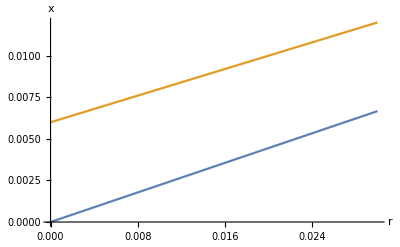

```mathematica
Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{r,0,μ},AxesLabel->{"r","x"},AxesOrigin->{0,0}]
```

### - μ

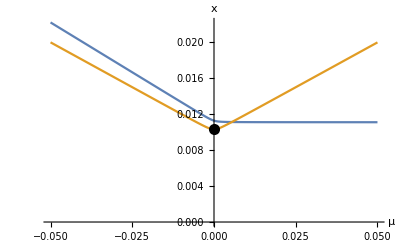

```mathematica
Show[Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{μ,-r,r},AxesLabel->{"μ","x"},AxesOrigin->{0,0}],
Graphics[{PointSize[0.02],Black,Point[{σ^2/2 ,xC[σ^2/2,σ,r,θ,δ]}]}]]
```

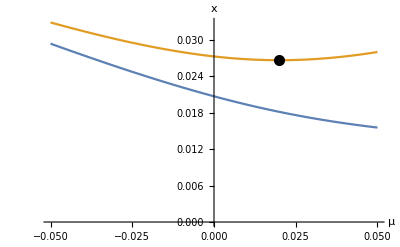

```mathematica
Module[{σ=0.2},
Show[Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{μ,-r,r},AxesLabel->{"μ","x"},AxesOrigin->{0,0}],
Graphics[{PointSize[0.02],Black,Point[{σ^2/2 ,xC[σ^2/2,σ,r,θ,δ]}]}]]
]
```

### - σ

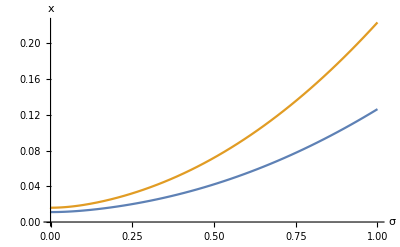

```mathematica
Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{σ,0,1},AxesLabel->{"σ","x"},AxesOrigin->{0,0}]
```

### - θ

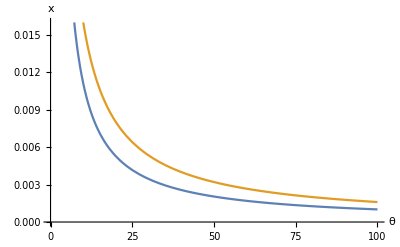

```mathematica
Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{θ,α k,100},AxesLabel->{"θ","x"},AxesOrigin->{0,0}]
```

### - δ

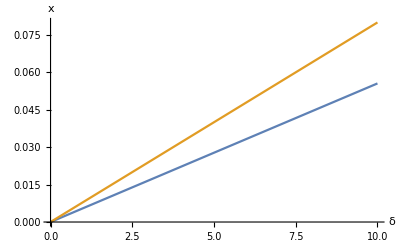

```mathematica
Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{δ,0,10},AxesLabel->{"δ","x"},AxesOrigin->{0,0}]
```

### - α

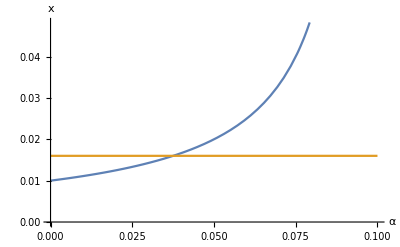

```mathematica
Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{α,0,θ/k},AxesLabel->{"α","x"},AxesOrigin->{0,0}]
```

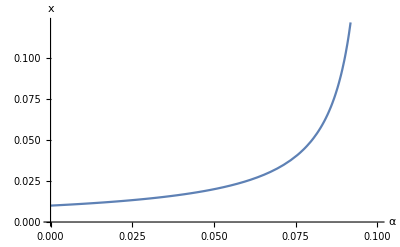

```mathematica
Plot[{xB[μ,σ,r,θ,k,α,δ]},{α,0,θ/k},AxesLabel->{"α","x"},AxesOrigin->{0,0}]
```

### - k

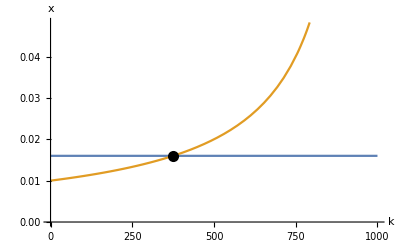

```mathematica
Show[Plot[{xC[μ,σ,r,θ,δ],xB[μ,σ,r,θ,k,α,δ]},{k,0,θ/α},AxesLabel->{"k","x"},AxesOrigin->{0,0}],
Graphics[{PointSize[0.02],Black,Point[{Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],xC[μ,σ,r,θ,δ]}]}]]
```

```mathematica
Module[{k1=100,k2=700(*k3=600,k4=700*)},
Show[Plot[{FxB[x,r,μ,σ,θ,α,δ,k1],FxB[x,r,μ,σ,θ,α,δ,k2],
(*FxB[x,r,μ,σ,θ,α,δ,k3],FxB[x,r,μ,σ,θ,α,δ,k4],*)
FxC[x ,r,μ,σ,θ,α,δ]},{x,0.001,0.1},PlotStyle->{Darker[Blue,.7],Blue,Orange},AxesLabel->{"x","F(x)"},AxesOrigin->{0,0},PlotLegends->Placed[{"F(x,K=100)","F(x,K=700)","F^*(x)"},{0.25,0.75}]],
Graphics[{PointSize[0.02],Black,Point[{xB[μ,σ,r,θ,k1,α,δ] ,FxB[xB[μ,σ,r,θ,k1,α,δ],r,μ,σ,θ,α,δ,k1]}]}],
Graphics[{PointSize[0.02],Black,Point[{xB[μ,σ,r,θ,k2,α,δ] ,FxB[xB[μ,σ,r,θ,k2,α,δ],r,μ,σ,θ,α,δ,k2]}]}],
(*Graphics[{PointSize[0.02],Black,Point[{xB[μ,σ,r,θ,k3,α,δ] ,FxB[xB[μ,σ,r,θ,k3,α,δ],r,μ,σ,θ,α,δ,k3]}]}],
Graphics[{PointSize[0.02],Black,Point[{xB[μ,σ,r,θ,k4,α,δ] ,FxB[xB[μ,σ,r,θ,k4,α,δ],r,μ,σ,θ,α,δ,k4]}]}],*)
Graphics[{PointSize[0.02],Black,Point[{xC[μ,σ,r,θ,δ] ,FxC[xC[μ,σ,r,θ,δ] ,r,μ,σ,θ,α,δ]}]}]
]]
```

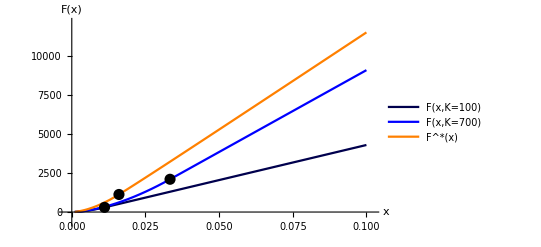

```mathematica
F_w
```

F_w

```mathematica
SuperStar[Subscript[x, B]]
```

```mathematica
SuperStar[F]
```

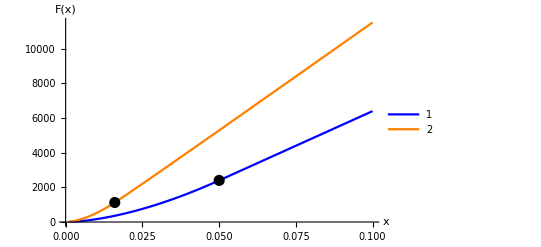

```mathematica
Module[{k1=800},
Show[Plot[{FxB[x,r,μ,σ,θ,α,δ,k1],FxC[x ,r,μ,σ,θ,α,δ]},{x,0.001,0.1},PlotStyle->{Blue,Orange},AxesLabel->{"x","F(x)"},AxesOrigin->{0,0},PlotLegends->"Placeholder"],
Graphics[{PointSize[0.02],Black,Point[{xB[μ,σ,r,θ,k1,α,δ] ,FxB[xB[μ,σ,r,θ,k1,α,δ],r,μ,σ,θ,α,δ,k1]}]}],
Graphics[{PointSize[0.02],Black,Point[{xC[μ,σ,r,θ,δ] ,FxC[xC[μ,σ,r,θ,δ] ,r,μ,σ,θ,α,δ]}]}]
]]
```

## - Optimal capacity K* and K*(x*)

#### - μ

```mathematica
Clear[xthreshold];
Kopt[μ_,r_,θ_,α_,δ_,x_]:=(θ x-δ(r-μ))/(2 α x);
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
xC[μ_,σ_,r_,θ_,δ_]:=(d1[μ,σ,r]+1)/(d1[μ,σ,r]-1) δ (r-μ)/θ;
```

```mathematica
Simplify@Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]]
```

(2 θ σ^2)/(α (-2 μ+(3+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))

```mathematica
Simplify@@{D[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],μ]}
```

(4 θ (-2 μ+(1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))/(α √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) (-2 μ+(3+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)^2)

```mathematica
Manipulate[Show[Plot[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],{μ,-r,r}]],{r,0.001,1},{σ,0.001,1},{δ,0.001,2},{k,1,100},{θ,1,10},{α,0.001,Min[θ/k]},FrameLabel->"μ"]
```

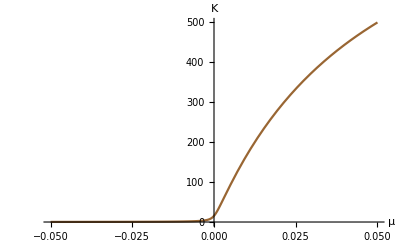

```mathematica
Show[Plot[{Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]]},{μ,-r,r},AxesLabel->{"μ","K"},AxesOrigin->{0,0},PlotStyle->Brown]]
```

#### - σ

```mathematica
Simplify@@{D[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],σ]}
```

-(8 θ (-2 μ^2-2 r σ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))/(α √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ (-2 μ+(3+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)^2)

```mathematica
Manipulate[Show[Plot[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],{σ,0.001,1},AxesLabel->{"σ","K*"}]],{r,0.001,1},{μ,-r,r},{δ,0.001,2},{k,1,100},{θ,1,10},{α,0.001,Min[θ/k]}]
```

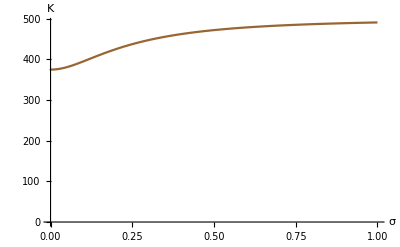

```mathematica
Show[Plot[{Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]]},{σ,0,1},AxesLabel->{"σ","K"},AxesOrigin->{0,0},PlotStyle->Brown]]
```

#### - r

```mathematica
D[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],r]
```

```mathematica
Manipulate[Show[Plot[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],{r,0.001,Abs[μ]},AxesLabel->{"r","K*"},AxesOrigin->{0,0}]],{σ,0.001,1},{μ,0,1},{δ,0.001,2},{k,1,100},{θ,1,10},{α,0.001,Min[θ/k]}]
```

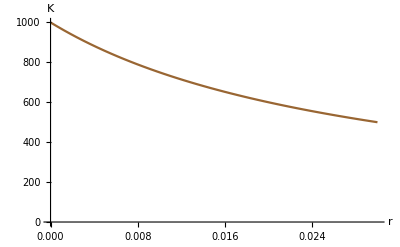

```mathematica
Show[Plot[{Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]]},{r,0,Abs[μ]},AxesLabel->{"r","K"},AxesOrigin->{0,0},PlotStyle->Brown]]
```

#### - δ

```mathematica
Manipulate[Show[Plot[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],{δ,0.001,2},AxesLabel->{"α","K*"},AxesOrigin->{0,0}]],{σ,0.001,1},{r,0.001,1},{k,1,100},{μ,-r,r},{θ,1,10},{α,0.001,Min[θ/k]}]
```

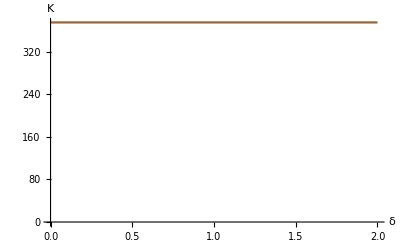

```mathematica
Show[Plot[{Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]]},{δ,0,2},AxesLabel->{"δ","K"},AxesOrigin->{0,0},PlotStyle->Brown]]
```

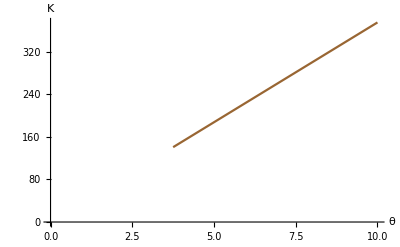

```mathematica
Show[Plot[{Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]]},{θ,α Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],10},AxesLabel->{"θ","K"},AxesOrigin->{0,0},PlotStyle->Brown]]
```

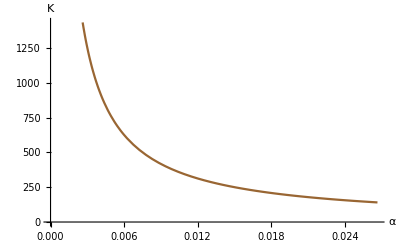

```mathematica
Show[Plot[{Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]]},{α,0.001,θ/Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]]},AxesLabel->{"α","K"},AxesOrigin->{0,0},PlotStyle->Brown]]
```

## Tests on ϕ

```mathematica
phi[r_,μ_,σ_]:=1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2;
```

```mathematica
Manipulate[Plot3D[phi[r,μ,σ],{μ,-r,r},{σ,0.001,1},AxesLabel->Automatic],{r,0.001,1}]
```

```mathematica
Solve[phi[r,μ,σ]==0,r]
```

{{r→(-4 μ^2+4 μ σ^2-σ^4)/(8 σ^2)}}

```mathematica
Solve[phi[r,μ,σ]==0,μ]
```

{{μ→1/2 σ (-2 ⅈ √2 √r+σ)},{μ→1/2 σ (2 ⅈ √2 √r+σ)}}

```mathematica
Solve[phi[r,μ,σ]==0,σ]
```

{{σ→-√2 √(-2 r-2 √(r (r-μ))+μ)},{σ→√2 √(-2 r-2 √(r (r-μ))+μ)},{σ→-√2 √(-2 r+2 √(r (r-μ))+μ)},{σ→√2 √(-2 r+2 √(r (r-μ))+μ)}}

```mathematica
D[phi[r,μ,σ],r]
```

8/σ^2

```mathematica
D[phi[r,μ,σ],μ]
```

(8 μ)/σ^4-4/σ^2

```mathematica
D[phi[r,μ,σ],σ]
```

-(16 μ^2)/σ^5-(16 r)/σ^3+(8 μ)/σ^3